# Point Force Greens Functions (force)

```mathematica
Get["/Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m"]
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*Log[r]
(*ex = D[Upt,x]
ey = D[Upt,y]*)
```

Get::noopen: Cannot open /Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m.

$Failed

Log[√((x-xs)^2+(y-ys)^2)]/(2 π)

## Integration over a constant source defined from y in [-W,W]

```mathematica
Uconst1d = Integrate[ReplaceAll[Upt,{ys->0}],{xs,-w,w},GenerateConditions->False]
(*Uconst1d =ReplaceAll[Uconst,{ys->w,xs->0}]-ReplaceAll[Uconst,{ys->-w,xs->0}]//FullSimplify*)
```

(-4 w+2 y (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+(w-x) Log[(w-x)^2+y^2]+(w+x) Log[(w+x)^2+y^2])/(4 π)

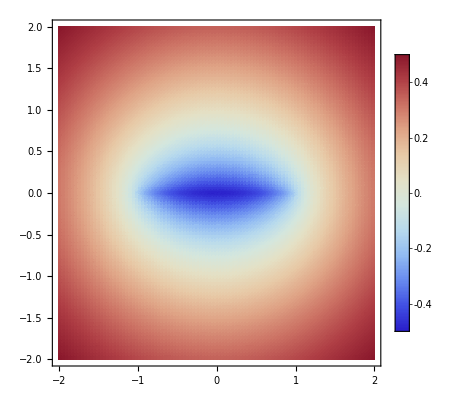

```mathematica
DensityPlot[ReplaceAll[Uconst1d,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->BarLegend[{Automatic,{-0.5,0.5}}],PlotPoints->100,PlotRange->{-0.5,0.5}]
```

## Integrate point source with linear force function over the domain y in [-W,W]

```mathematica
ULinB1 = Integrate[Upt*(1+1/w*xs)/2,xs,GeneratedParameters->C];
ULinB2 = Integrate[Upt*(1-1/w*xs)/2,xs,GeneratedParameters->C];
ULin1dB1 =ReplaceAll[ULinB1,{xs->w,ys->0}]-ReplaceAll[ULinB1,{xs->-w,ys->0}]//FullSimplify;
ULin1dB2 =ReplaceAll[ULinB2,{xs->w,ys->0}]-ReplaceAll[ULinB2,{xs->-w,ys->0}]//FullSimplify;
ToMatlab[ULin1dB1]
ToMatlab[ULin1dB1/. ArcTan[x_/y_] :> ArcTan[y,x]]
ToMatlab[ULin1dB2]
```

(1/16).*pi.^(-1).*w.^(-1).*((-4).*w.*(2.*w+x)+4.*(w+x).*y.*atan(( ...
  w+(-1).*x).*y.^(-1))+4.*(w+x).*y.*atan((w+x).*y.^(-1))+((w+(-1).* ...
  x).*(3.*w+x)+y.^2).*log((w+(-1).*x).^2+y.^2)+(w+x+(-1).*y).*(w+x+ ...
  y).*log((w+x).^2+y.^2));

(1/16).*pi.^(-1).*w.^(-1).*((-4).*w.*(2.*w+x)+4.*(w+x).*y.*atan2( ...
  w+(-1).*x, y)+4.*(w+x).*y.*atan2(w+x, y)+((w+(-1).*x).*(3.*w+x)+ ...
  y.^2).*log((w+(-1).*x).^2+y.^2)+(w+x+(-1).*y).*(w+x+y).*log((w+x) ...
  .^2+y.^2));

(1/16).*pi.^(-1).*w.^(-1).*(4.*w.*((-2).*w+x)+4.*(w+(-1).*x).*y.* ...
  atan((w+(-1).*x).*y.^(-1))+4.*(w+(-1).*x).*y.*atan((w+x).*y.^(-1)) ...
  +(w+(-1).*x+(-1).*y).*(w+(-1).*x+y).*log((w+(-1).*x).^2+y.^2)+(( ...
  3.*w+(-1).*x).*(w+x)+y.^2).*log((w+x).^2+y.^2));

```mathematica
DensityPlot[{ReplaceAll[ULin1dB1,{w->1}],ReplaceAll[ULin1dB2,{w->1}]},{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->{-1,1},PlotPoints->100,PlotRange->{-0.5,0.5}]
```

-Graphics-

```mathematica
exB1 = D[ULin1dB1,x]//FullSimplify
exB2 = D[ULin1dB2,x]//FullSimplify
eyB1 = D[ULin1dB1,y]//FullSimplify
eyB2 = D[ULin1dB2,y]//FullSimplify
```

(-4 w+2 y (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])-(w+x) Log[(w-x)^2+y^2]+(w+x) Log[(w+x)^2+y^2])/(4 π w)

-(-4 w+2 y (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+(w-x) (Log[(w-x)^2+y^2]-Log[(w+x)^2+y^2]))/(4 π w)

(2 (w+x) (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+y (Log[(w-x)^2+y^2]-Log[(w+x)^2+y^2]))/(4 π w)

(2 (w-x) (ArcTan[(w-x)/y]+ArcTan[(w+x)/y])+y (-Log[(w-x)^2+y^2]+Log[(w+x)^2+y^2]))/(4 π w)

```mathematica
ToMatlab[exB1]
ToMatlab[exB2]
ToMatlab[eyB1]
ToMatlab[eyB2]
```

(1/4).*pi.^(-1).*w.^(-1).*((-4).*w+2.*y.*(atan((w+(-1).*x).*y.^( ...
  -1))+atan((w+x).*y.^(-1)))+(-1).*(w+x).*log((w+(-1).*x).^2+y.^2)+( ...
  w+x).*log((w+x).^2+y.^2));

(-1/4).*pi.^(-1).*w.^(-1).*((-4).*w+2.*y.*(atan((w+(-1).*x).*y.^( ...
  -1))+atan((w+x).*y.^(-1)))+(w+(-1).*x).*(log((w+(-1).*x).^2+y.^2)+ ...
  (-1).*log((w+x).^2+y.^2)));

(1/4).*pi.^(-1).*w.^(-1).*(2.*(w+x).*(atan((w+(-1).*x).*y.^(-1))+ ...
  atan((w+x).*y.^(-1)))+y.*(log((w+(-1).*x).^2+y.^2)+(-1).*log((w+x) ...
  .^2+y.^2)));

(1/4).*pi.^(-1).*w.^(-1).*(2.*(w+(-1).*x).*(atan((w+(-1).*x).*y.^( ...
  -1))+atan((w+x).*y.^(-1)))+y.*((-1).*log((w+(-1).*x).^2+y.^2)+log( ...
  (w+x).^2+y.^2)));

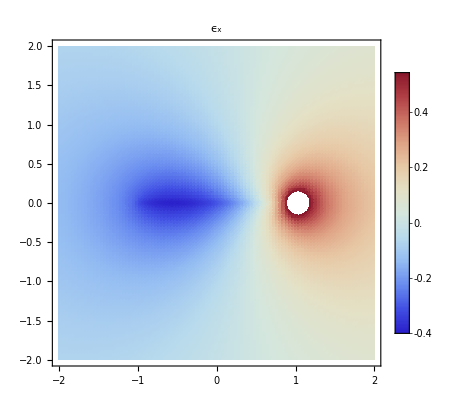

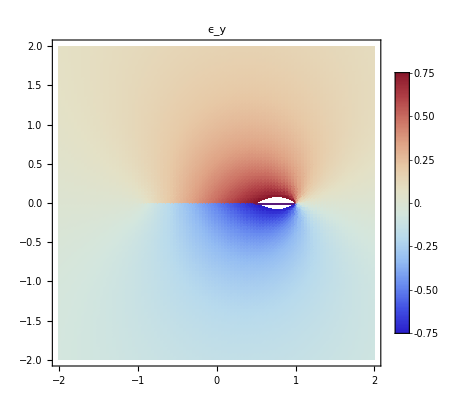

```mathematica
DensityPlot[ReplaceAll[exB1,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100,PlotLabel->Subscript[ϵ, x]]
DensityPlot[ReplaceAll[eyB1,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100,PlotRange->{-0.75,0.75},PlotLabel->Subscript[ϵ, y]]
```

## Plot a cross section of displacements and stresses at x = 0

```mathematica
yeval=0.000001;
weval = 1;
Plot[ReplaceAll[ULin1dB1,{w->weval,y->yeval}],{x,-2,2},PlotLabels->"displacement",Filling->Axis,AxesLabel->{x,u[x]},PlotStyle->{Thick,Black}]
Plot[{ReplaceAll[exB1,{w->weval,y->yeval}],ReplaceAll[eyB1,{w->weval,y->yeval}]},{x,-2,2},AxesLabel->{x,Stress},PlotLabels->{Subscript[σ, x],Subscript[σ, y]}]
```

-Graphics-

-Graphics-

## Solve 2-d indefinite integral and insert limits to solve definite integral

### Displacement field

-(3 w (l-x/w))/(4 π)-((l-x/w) y ArcTan[(l-x/w-y)/x])/(4 π)+((l-x/w) y ArcTan[(l-x/w-y)/(-w+x)])/(4 π)+(y^2 ArcTan[x/y])/(2 π)-(y^2 ArcTan[(-w+x)/y])/(2 π)+((x^2+y^2) ArcTan[y/x])/(4 π)-((w^2-2 w x+x^2+y^2) ArcTan[y/(-w+x)])/(4 π)-((-l+x/w+y)^2 ArcTan[x/(-l+x/w+y)])/(2 π)+((-l+x/w+y)^2 ArcTan[(-w+x)/(-l+x/w+y)])/(2 π)-((x^2+(l-x/w)^2-(l-x/w) y+y^2) ArcTan[(-l+x/w+y)/x])/(4 π)+((w^2-2 w x+x^2+(l-x/w)^2-(l-x/w) y+y^2) ArcTan[(-l+x/w+y)/(-w+x)])/(4 π)+(x y Log[x^2+y^2])/(4 π)+((w y)/(4 π)-(x y)/(4 π)) Log[(-w+x)^2+y^2]+((x (l-x/w))/(4 π)-(x y)/(4 π)) Log[x^2+(-l+x/w+y)^2]+((w (l-x/w))/(4 π)-(x (l-x/w))/(4 π)-(w y)/(4 π)+(x y)/(4 π)) Log[(-w+x)^2+(-l+x/w+y)^2]

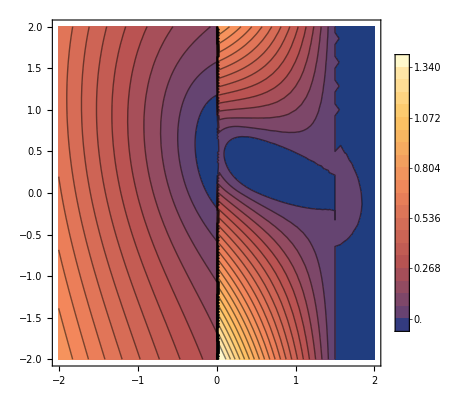

```mathematica
uIndefx = Integrate[Upt,xs,ys,GeneratedParameters->C];
uDefx = ReplaceAll[uIndefx,{xs->w}]-ReplaceAll[uIndefx,{xs->0}];
uDef = ReplaceAll[uDefx,{ys->l-x/w}]-ReplaceAll[uDefx,{ys->0}];(*/Collect[%,{ArcTan,Log}]*)
Collect[uDef,{ArcTan[x_,y_],Log[x_]}]
ContourPlot[ReplaceAll[uDef,{w->1.5,l->1}],{x,-2,2},{y,-2,2},PlotLegends->Automatic,Contours->21]
```

### Integrate Strains

```mathematica
uxIndefx = Integrate[D[Upt,x],xs,ys,GeneratedParameters->C];
uxDefx = ReplaceAll[uxIndefx,{xs->w}]-ReplaceAll[uxIndefx,{xs->0}];
uxDef = ReplaceAll[uxDefx,{ys->l-x/w}]-ReplaceAll[uxDefx,{ys->0}];(*/Collect[%,{ArcTan,Log}]*)
Collect[uxDef,{ArcTan[_,_],Log[_]}]
uyIndefx = Integrate[D[Upt,y],xs,ys,GeneratedParameters->C];
uyDefx = ReplaceAll[uyIndefx,{xs->w}]-ReplaceAll[uyIndefx,{xs->0}];
uyDef = ReplaceAll[uyDefx,{ys->l-x/w}]-ReplaceAll[uyDefx,{ys->0}];(*/Collect[%,{ArcTan,Log}]*)
Collect[uyDef,{ArcTan[x_,y_],x,Log[x_]}]
wval=1.5;
ContourPlot[{ReplaceAll[uxDef,{w->wval,l->1}],ReplaceAll[uyDef,{w->wval,l->1}]},{x,-2,2},{y,-2,2},PlotLegends->Automatic,Contours->21]
```

-(x ArcTan[x/y])/(2 π)+(x ArcTan[(-w+x)/y])/(2 π)+(w ArcTan[y/(-w+x)])/(2 π)+(x ArcTan[x/(-l+x/w+y)])/(2 π)-(x ArcTan[(-w+x)/(-l+x/w+y)])/(2 π)-(w ArcTan[(-l+x/w+y)/(-w+x)])/(2 π)+(y Log[x^2+y^2])/(4 π)-(y Log[w^2-2 w x+x^2+y^2])/(4 π)+((l-x/w-y) Log[x^2+(-l+x/w+y)^2])/(4 π)-((l-x/w-y) Log[w^2-2 w x+x^2+(-l+x/w+y)^2])/(4 π)

(y ArcTan[x/y])/(2 π)-(y ArcTan[(-w+x)/y])/(2 π)+(l ArcTan[x/(-l+x/w+y)])/(2 π)-(y ArcTan[x/(-l+x/w+y)])/(2 π)-(l ArcTan[(-w+x)/(-l+x/w+y)])/(2 π)+(y ArcTan[(-w+x)/(-l+x/w+y)])/(2 π)+(w Log[w^2-2 w x+x^2+y^2])/(4 π)-(w Log[w^2-2 w x+x^2+(-l+x/w+y)^2])/(4 π)+x (-ArcTan[x/(-l+x/w+y)]/(2 π w)+ArcTan[(-w+x)/(-l+x/w+y)]/(2 π w)+Log[x^2+y^2]/(4 π)-Log[w^2-2 w x+x^2+y^2]/(4 π)-Log[x^2+(-l+x/w+y)^2]/(4 π)+Log[w^2-2 w x+x^2+(-l+x/w+y)^2]/(4 π))

-Graphics-

## Integrate point source over a 2-d triangle domain (this is not a useful route!)

```mathematica
vertices={{0,0},{w,0},{0,l}};
(*Step 2:Define the function to integrate*)
fu=Upt;
fux =D[Upt,x];
fuy =D[Upt,y];
(*Step 3:Define the region of integration*)
region=Triangle[vertices];
(*region = Rectangle[{0,0},{w,l}];*)
(*Step 4:Perform the integration*)
uTri=Integrate[fu,{xs,ys}∈region]/. ArcTan[x_/y_] :> ArcTan[y,x];
uxTri=Integrate[fux,{xs,ys}∈region];(*%/. ArcTan[x_/y_] :> ArcTan[y,x]*)
uyTri=Integrate[fuy,{xs,ys}∈region];(*/. ArcTan[x_/y_] :> ArcTan[y,x];*)
```

## Simplification and combine similar terms (ArcTan rules)

```mathematica
(*arctanRule[x_,y_]:=
If[x*y<=1,ArcTan[(x+y)/(1-x*y)],
If[x>0&&y>0,ArcTan[(x+y)/(1-x*y)]+Pi,
If[x<0&&y<0,ArcTan[(x+y)/(1-x*y)]-Pi]
]
]*)
arctanRule[x_,y_]:=ArcTan[(x+y)/(1-x*y)]
(*arctanRule[x_,y_]:=Which[
x*y<=1,ArcTan[(x+y)/(1-x*y)],
x>0&&y>0&&x*y>1,ArcTan[(x+y)/(1-x*y)]+Pi,
x<0&&y<0&&x*y>1,ArcTan[(x+y)/(1-x*y)]-Pi
]*)
(*uTriMod=Collect[uTri,{Abs[x_],ArcTan[x_,y_],1/(4l Pi),Log[x_]}];*)
uxTriMod=Collect[uxTri,{Abs[x_],(l^2+w^2),(l^2+w x-l y)ArcTan,Log[x_]},Simplify]
uxVal = uxTriMod/. ArcTan[x_]+ArcTan[y_]:>arctanRule[x,y]//Simplify
(*PrintMatlab[uTri]/. ArcTan[x_/y_] :> ArcTan[y,x]*)
ToMatlab[uxVal/. ArcTan[x_/y_] :> ArcTan[y,x]]
(*PrintMatlab[uyTri]*)
```

Abs[l w] (-(x (ArcTan[(w-x)/y]+ArcTan[x/y]))/(2 l π w)-(y Log[(w-x)^2+y^2])/(4 l π w)+(((l^2+w x-l y) (ArcTan[(l w-l x-w y)/(l^2+w x-l y)]+ArcTan[(l w-l x-w y)/(w^2-w x+l y)]))/(2 l π)+((l w-l x-w y) Log[x^2+(l-y)^2])/(4 l π)+((l (-w+x)+w y) Log[(w-x)^2+y^2])/(4 l π))/(l^2+w^2)+(y Log[x^2+y^2])/(4 l π w))

1/(4 l π w (l^2+w^2))Abs[l w] (2 w (l^2+w x-l y) ArcTan[(l (w-x)-w y)/(w x-x^2+(l-y) y)]-2 (l^2+w^2) x ArcTan[(w y)/(-w x+x^2+y^2)]+l w^2 Log[x^2+(l-y)^2]-l w x Log[x^2+(l-y)^2]-w^2 y Log[x^2+(l-y)^2]-l w^2 Log[(w-x)^2+y^2]+l w x Log[(w-x)^2+y^2]-l^2 y Log[(w-x)^2+y^2]+l^2 y Log[x^2+y^2]+w^2 y Log[x^2+y^2])

(1/4).*l.^(-1).*pi.^(-1).*w.^(-1).*(l.^2+w.^2).^(-1).*abs(l.*w).*( ...
  2.*w.*(l.^2+w.*x+(-1).*l.*y).*atan2(l.*(w+(-1).*x)+(-1).*w.*y, w.* ...
  x+(-1).*x.^2+(l+(-1).*y).*y)+(-2).*(l.^2+w.^2).*x.*atan2(w.*y, ( ...
  -1).*w.*x+x.^2+y.^2)+l.*w.^2.*log(x.^2+(l+(-1).*y).^2)+(-1).*l.* ...
  w.*x.*log(x.^2+(l+(-1).*y).^2)+(-1).*w.^2.*y.*log(x.^2+(l+(-1).*y) ...
  .^2)+(-1).*l.*w.^2.*log((w+(-1).*x).^2+y.^2)+l.*w.*x.*log((w+(-1) ...
  .*x).^2+y.^2)+(-1).*l.^2.*y.*log((w+(-1).*x).^2+y.^2)+l.^2.*y.* ...
  log(x.^2+y.^2)+w.^2.*y.*log(x.^2+y.^2));

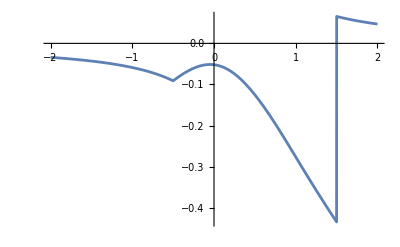

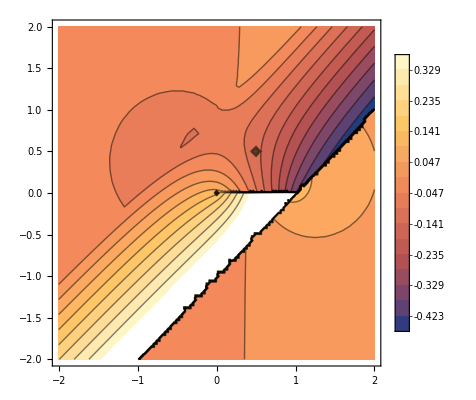

```mathematica
Plot[ReplaceAll[uxVal,{w->1,l->1,y->0.5}],{x,-2,2}]
ContourPlot[ReplaceAll[uxVal,{w->1,l->1}],{x,-2,2},{y,-2,2},PlotLegends->Automatic,Contours->21]
```